```mathematica
(*Definición de matrices w*)
w={DiagonalMatrix[{1,-1,1}],DiagonalMatrix[{1,1,-1}], DiagonalMatrix[{-1,1,1}],DiagonalMatrix[{-1,-1,-1}]};
(*Definición de las funciones de distancia*)
TrDist[r_,s_]:=Sqrt[(r-s).(r-s)]/2;
Fid[r_,s_]:=(1+r.s)/2;
Aff[r_,s_]:=(r.s+(1+Sqrt[1-r.r]) (1+Sqrt[1-s.s]))/((Sqrt[1+Sqrt[r.r]]+Sqrt[1-Sqrt[r.r]]) (Sqrt[1+Sqrt[s.s]]+Sqrt[1-Sqrt[s.s]]));
WootersDist[r_,s_] := ArcCos[Sqrt[Fid[r, s]]];
Distances = {
{TrDist, "Trace Distance",N[8(11−2√10)/81]}, 
{Fid, "Fidelity",N[2/3]}, 
{Aff, "Affinity",N[√5/3] }, 
{WootersDist, "Wooters Distance",0.589}
};
```

```mathematica
(*Definición de los canales ruidosos*)
adM[x_]:=DiagonalMatrix[{Sqrt[1-x],Sqrt[1-x],1-x}];
adC[x_]:={0,0,x};
madM[x_]:=DiagonalMatrix[{Sqrt[1-x],Sqrt[1-x],1-x}];
madC[x_]:={0,0,-x};
deM[x_]:=DiagonalMatrix[{1-x,1-x,1-x}];
deC[x_]:={0,0,0};
Channels = {{adM, adC, "Amplitude Damping"}, {madM, madC, "Mirrored Amplitude Damping"}, {deM, deC, "Depolarizing"}};
```

{0,1/10,1/5,3/10,2/5,0.461772,1/2,3/5,7/10}

{{},{},{},{},{},{RGBColor[0, 0, 1],Dashing[{Small,Small}]},{},{},{}}

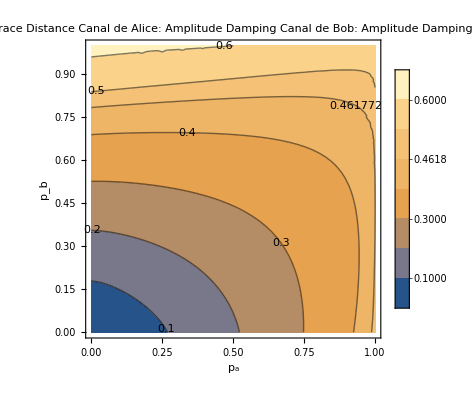

{1/2,3/5,0.666667,7/10,4/5,9/10,1,11/10}

{{},{},{RGBColor[0, 0, 1],Dashing[{Small,Small}]},{},{},{},{},{}}

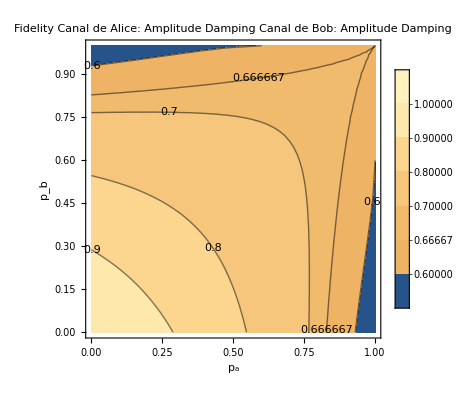

{1/2,3/5,7/10,0.745356,4/5,9/10,1,11/10}

{{},{},{},{RGBColor[0, 0, 1],Dashing[{Small,Small}]},{},{},{},{}}

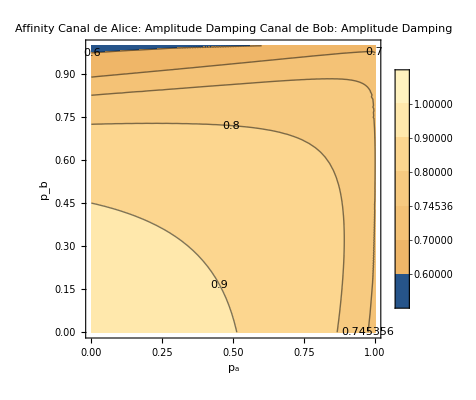

{0,1/10,1/5,3/10,2/5,1/2,0.589,3/5,7/10,4/5}

{{},{},{},{},{},{},{RGBColor[0, 0, 1],Dashing[{Small,Small}]},{},{},{}}

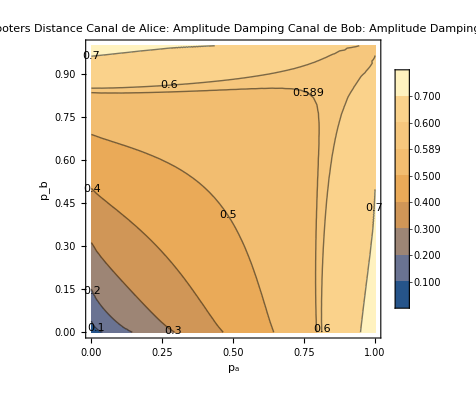

{0,1/10,1/5,3/10,2/5,0.461772,1/2,3/5}

{{},{},{},{},{},{RGBColor[0, 0, 1],Dashing[{Small,Small}]},{},{}}

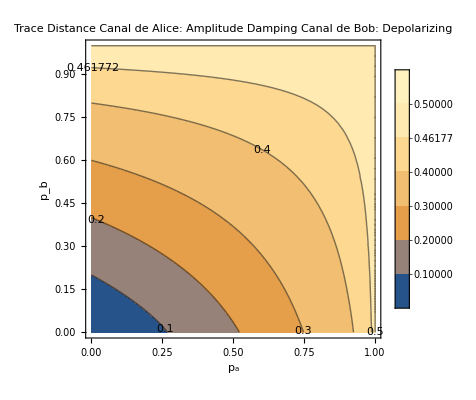

{1/2,3/5,0.666667,7/10,4/5,9/10,1,11/10}

{{},{},{RGBColor[0, 0, 1],Dashing[{Small,Small}]},{},{},{},{},{}}

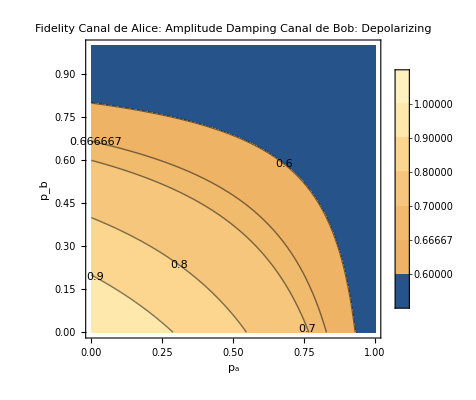

{7/10,0.745356,3/4,4/5,17/20,9/10,19/20,1,21/20}

{{},{RGBColor[0, 0, 1],Dashing[{Small,Small}]},{},{},{},{},{},{},{}}

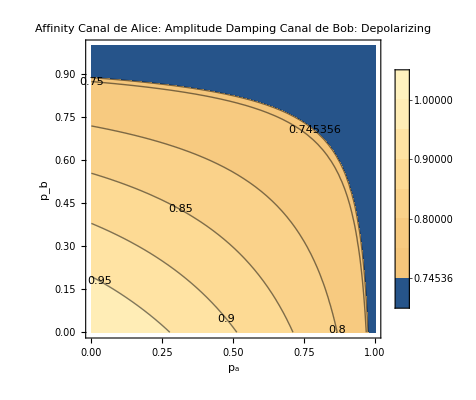

{0,1/10,1/5,3/10,2/5,1/2,0.589,3/5,7/10,4/5}

{{},{},{},{},{},{},{RGBColor[0, 0, 1],Dashing[{Small,Small}]},{},{},{}}

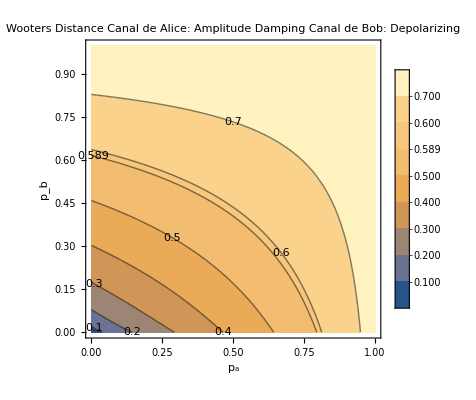

{0,1/10,1/5,3/10,2/5,0.461772,1/2,3/5,7/10}

{{},{},{},{},{},{RGBColor[0, 0, 1],Dashing[{Small,Small}]},{},{},{}}

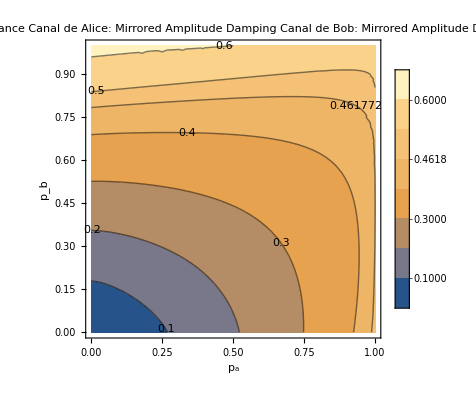

{1/2,3/5,0.666667,7/10,4/5,9/10,1,11/10}

{{},{},{RGBColor[0, 0, 1],Dashing[{Small,Small}]},{},{},{},{},{}}

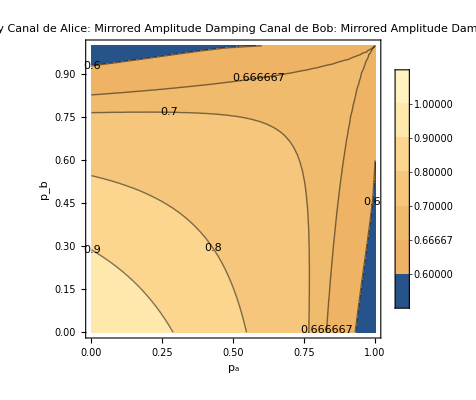

{1/2,3/5,7/10,0.745356,4/5,9/10,1,11/10}

{{},{},{},{RGBColor[0, 0, 1],Dashing[{Small,Small}]},{},{},{},{}}

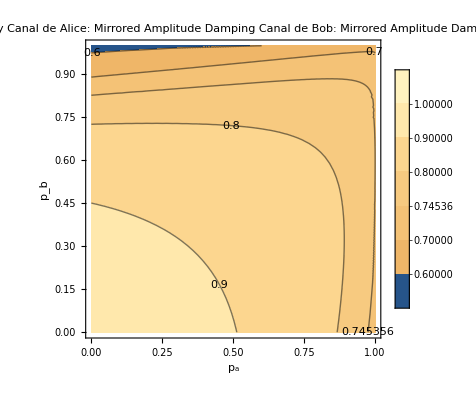

{0,1/10,1/5,3/10,2/5,1/2,0.589,3/5,7/10,4/5}

{{},{},{},{},{},{},{RGBColor[0, 0, 1],Dashing[{Small,Small}]},{},{},{}}

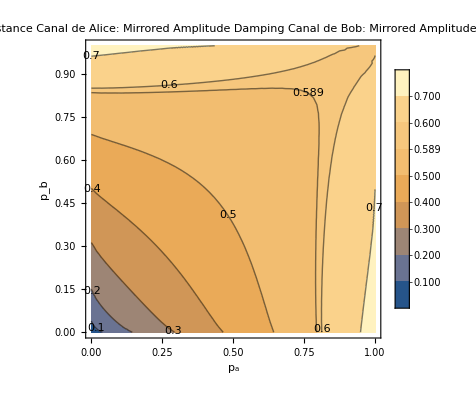

{0,1/10,1/5,3/10,2/5,0.461772,1/2,3/5}

{{},{},{},{},{},{RGBColor[0, 0, 1],Dashing[{Small,Small}]},{},{}}

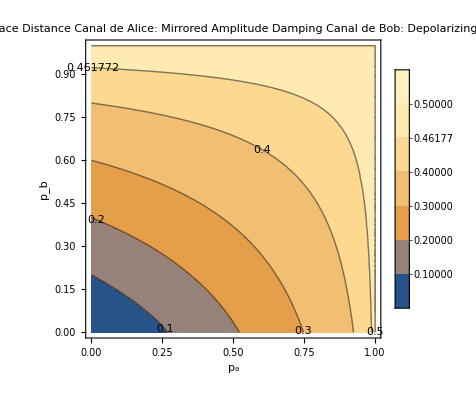

{1/2,3/5,0.666667,7/10,4/5,9/10,1,11/10}

{{},{},{RGBColor[0, 0, 1],Dashing[{Small,Small}]},{},{},{},{},{}}

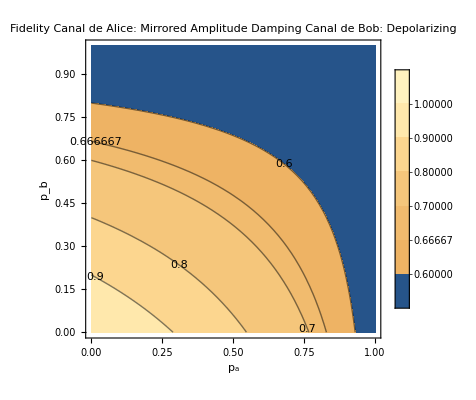

{7/10,0.745356,3/4,4/5,17/20,9/10,19/20,1,21/20}

{{},{RGBColor[0, 0, 1],Dashing[{Small,Small}]},{},{},{},{},{},{},{}}

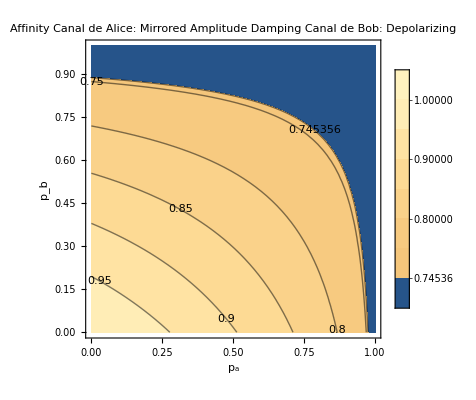

{0,1/10,1/5,3/10,2/5,1/2,0.589,3/5,7/10,4/5}

{{},{},{},{},{},{},{RGBColor[0, 0, 1],Dashing[{Small,Small}]},{},{},{}}

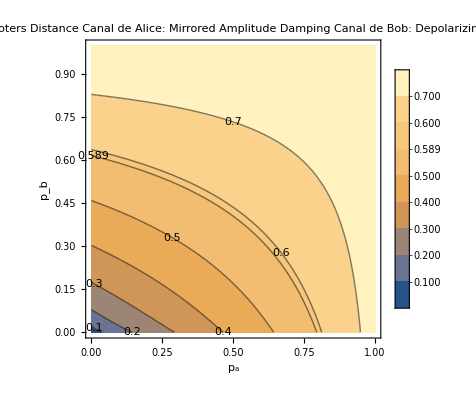

{0,1/10,1/5,3/10,2/5,0.461772,1/2,3/5,7/10}

{{},{},{},{},{},{RGBColor[0, 0, 1],Dashing[{Small,Small}]},{},{},{}}

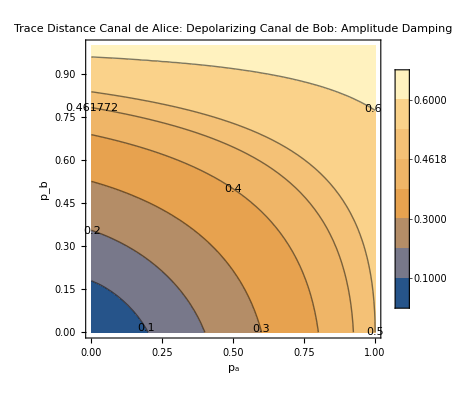

{1/2,3/5,0.666667,7/10,4/5,9/10,1,11/10}

{{},{},{RGBColor[0, 0, 1],Dashing[{Small,Small}]},{},{},{},{},{}}

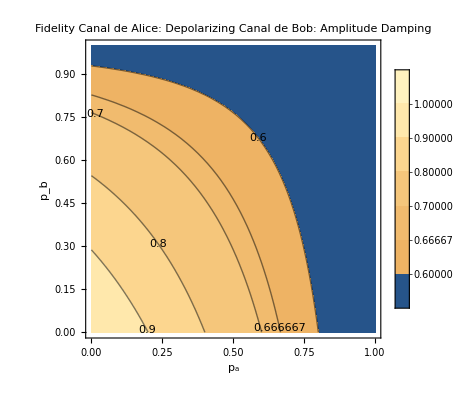

{1/2,3/5,7/10,0.745356,4/5,9/10,1,11/10}

{{},{},{},{RGBColor[0, 0, 1],Dashing[{Small,Small}]},{},{},{},{}}

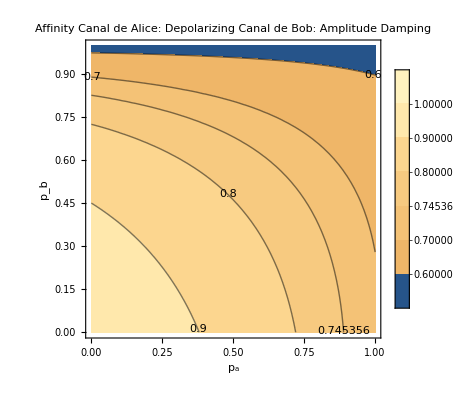

{0,1/10,1/5,3/10,2/5,1/2,0.589,3/5,7/10,4/5}

{{},{},{},{},{},{},{RGBColor[0, 0, 1],Dashing[{Small,Small}]},{},{},{}}

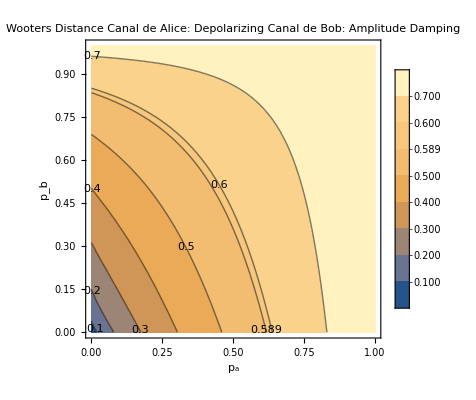

{0,1/10,1/5,3/10,2/5,0.461772,1/2,3/5,7/10}

{{},{},{},{},{},{RGBColor[0, 0, 1],Dashing[{Small,Small}]},{},{},{}}

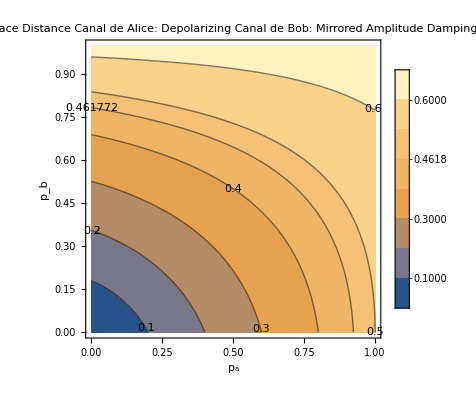

{1/2,3/5,0.666667,7/10,4/5,9/10,1,11/10}

{{},{},{RGBColor[0, 0, 1],Dashing[{Small,Small}]},{},{},{},{},{}}

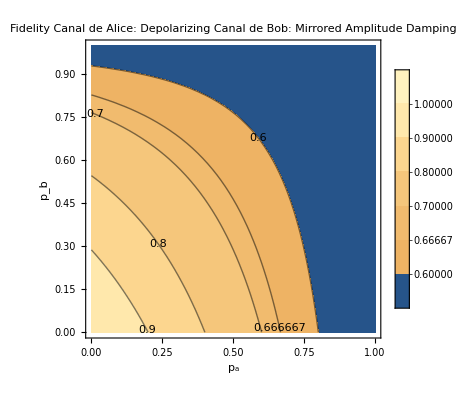

{1/2,3/5,7/10,0.745356,4/5,9/10,1,11/10}

{{},{},{},{RGBColor[0, 0, 1],Dashing[{Small,Small}]},{},{},{},{}}

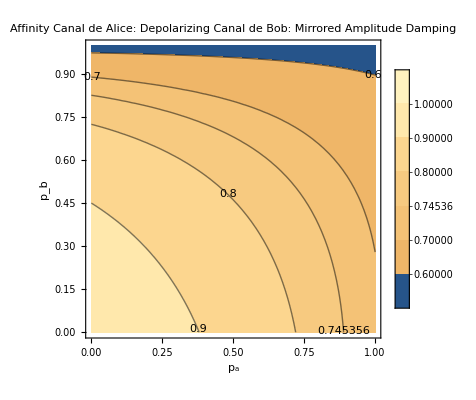

{0,1/10,1/5,3/10,2/5,1/2,0.589,3/5,7/10,4/5}

{{},{},{},{},{},{},{RGBColor[0, 0, 1],Dashing[{Small,Small}]},{},{},{}}

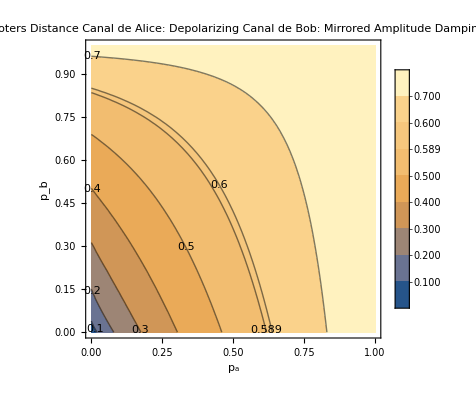

{0,1/10,1/5,3/10,2/5,0.461772,1/2,3/5}

{{},{},{},{},{},{RGBColor[0, 0, 1],Dashing[{Small,Small}]},{},{}}

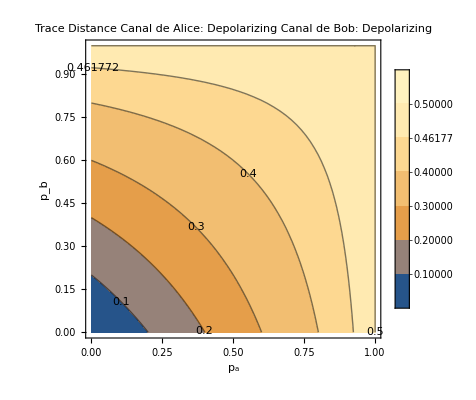

{1/2,3/5,0.666667,7/10,4/5,9/10,1,11/10}

{{},{},{RGBColor[0, 0, 1],Dashing[{Small,Small}]},{},{},{},{},{}}

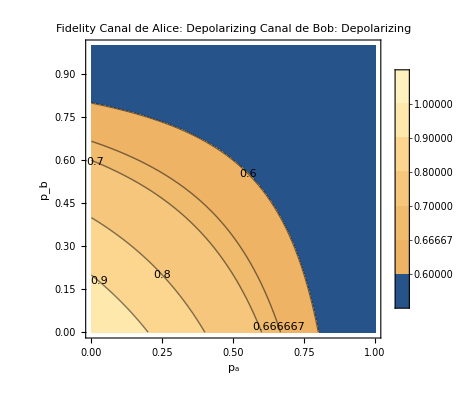

{7/10,0.745356,3/4,4/5,17/20,9/10,19/20,1,21/20}

{{},{RGBColor[0, 0, 1],Dashing[{Small,Small}]},{},{},{},{},{},{},{}}

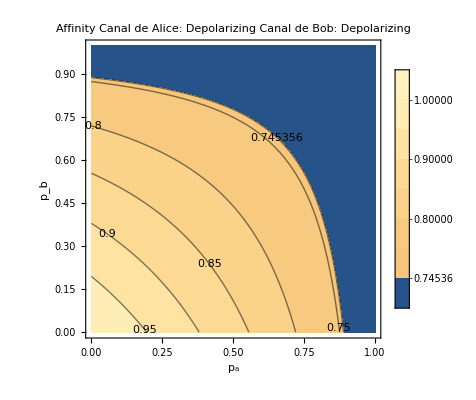

{0,1/10,1/5,3/10,2/5,1/2,0.589,3/5,7/10,4/5}

{{},{},{},{},{},{},{RGBColor[0, 0, 1],Dashing[{Small,Small}]},{},{},{}}

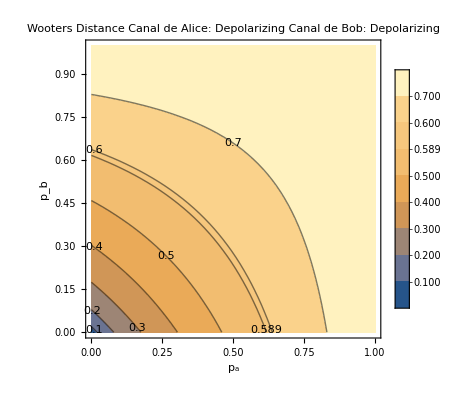

```mathematica
Do[
Do[
If[(chA[[3]] == "Amplitude Damping" && chB[[3]] == "Mirrored Amplitude Damping") || (chB[[3]] == "Amplitude Damping" && chA[[3]] == "Mirrored Amplitude Damping"), Continue[]]
(*Matriz de correlación de la forma de Fano de un par de Bell pasado por dos canales ruidosos*)
r=chA[[1]][pA].w[[1]].chB[[1]][pB]+Outer[Times,chA[[2]][pA],chB[[2]][pB]];
(*Vectores de Bloch de los estados reducidos de Alice y Bob*)
rA=chA[[2]][pA];
     rB=chB[[2]][pB];

(*rDiag=Diagonal[r]; (*puedo hacer esto porque en este caso siempre es diagonal r, no hace falta diagonalizarlo*)
M:=(Prepend[r,1].Table[KroneckerProduct[PauliMatrix[i],PauliMatrix[i]],{i,0,3}])/4;
maxEigenstate = Eigensystem[M][[2]][[4]]; (* para Amplitude Damping vs. Mirrored Amplitude Damping y viceversa hay que generar los graficos de otra forma porque el maximo autovalor depende de pA y pB*)*)

lmax = 1;(*para todos los casos menos Amplitude Damping vs. Mirrored Amplitude Damping (que hay que hacerlos de otra forma) lmax vale 1*)

RotOptFid[i_]:=w[[i]].w[[lmax]];

(*Definición de t,p[i] y tBob[i]*)
t={Cos[ϕ]*Sin[θ],Sin[ϕ]*Sin[θ],Cos[θ]};
     p[i_]:=(1+t.(w[[i]].rA))/4;
     tBob[i_]:=1/(4*p[i])*RotOptFid[i].(rB+Transpose[w[[i]].r].t);


Do[
(*Definición de AvgDist*)
AvgDist[pA_,pB_]:=1/(4 Pi) NIntegrate[Evaluate[Sum[p[i]*d[[1]][t,tBob[i]],{i,1,4}]*Sin[θ]],{ϕ,0,2 Pi},{θ,0,Pi}];

(*ContourPlot*)
plot =ContourPlot[AvgDist[pA,pB],{pA,0,1},{pB,0,1},
FrameLabel->{Style[Subscript[p,a],Black,Italic,24],Style[Subscript[p,b],Black,Italic,24]},
Contours->((contours = Sort[Append[FindDivisions[{#1,#2},#3], d[[3]]]])&),
(*Contours->((contours = Join[FindDivisions[{#1, d[[3]]},Quotient[#3,2]],{d[[3]]},  FindDivisions[{d[[3]],#2},Quotient[#3,2]-1]])&),*)
ContourLabels->All,
PlotLegends->Automatic, 
PlotLabel-> d[[2]] <> "\nCanal de Alice: " <> chA[[3]] <> "\nCanal de Bob: " <> chB[[3]] 
];
estilosDeContornos = Map[(If[# == d[[3]], {Blue,Dashed}, {}]&), contours];
Print[contours];
Print[estilosDeContornos];
Print[Show[plot, ContourStyle->estilosDeContornos]];
 
,{d, Distances}]
,{chB, Channels}]
,{chA, Channels}]
```